```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
μ0 = 3.8284
```

3.8284

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
im = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

```mathematica
ys =FullSimplify[ Solve[im==0,y]]
```

```mathematica
xs = Solve[im==0,x];
```

```mathematica
x0s =Select[Flatten[xs/.{μ-> μ0, y-> 0}],# ⟦2⟧<0.5&];
```

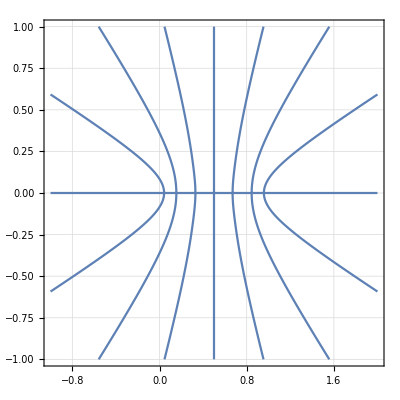

```mathematica
imμ =im/.μ-> μ0;
ContourPlot[imμ== 0,{x,-1,2},{y,-1,1},GridLines->Automatic, MaxRecursion->5]
```

```mathematica
rlist={};
Do[AppendTo[rlist, FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦i,1,2⟧/.{y-> ys⟦i,1,2⟧}/.x-> x0 ]/.μ-> μ0],{i,2,7}];
```

```mathematica
ϵlist = {};
Do[AppendTo[ϵlist, Reduce[Abs[rlist⟦i⟧]== 1,ϵ,Reals]],{i,1,6}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Abs[ϵmax].

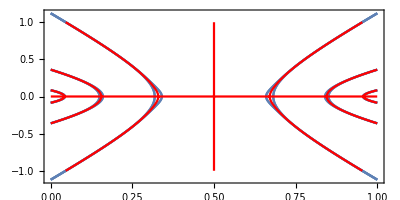

```mathematica
dp = 0;
up  = 1;
pplots={};
pplotsmin={};
pplotsmax={};

Do[
localpplotsmin={};
localpplotsmax={};
i=n-1;
f=StringLength[ToString[#]]&;
nonesquad = {};
group = SortBy[Chop[ϵlist⟦i⟧,10^-5],f];
strlen = Table[StringLength[ToString[group⟦k⟧]],{k,1,Length[ϵlist⟦i⟧]}];
Do[If[strlen⟦m⟧<100,AppendTo[nonesquad,m],None], {m,1,Length[ϵlist⟦i⟧]}];
ig = Range[Length[group]];
ig = Drop[ig,Length[nonesquad]];

Do[
ysn = ys⟦n,1,2⟧/.{μ-> μ0,x-> x0};
Which[
j== ig⟦1⟧,d=1.00001group⟦j,1,2⟧; u=1,
j== ig⟦2⟧, d=0;u=0.9999group⟦j,1,2⟧,
j> ig⟦2⟧, d= 1.00001group⟦j,1,1⟧;u=0.999999group⟦j,1,5⟧];
part1 = group⟦j,2,1,2⟧;
part2 = group⟦j,2,2,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part1, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part1, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0+part2, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part2, ysn},{x0,d,u},PlotRange->{{dp,up},All},Frame->True,MaxRecursion->5]];

AppendTo[localpplotsmin,Table[{ysn, x0+part1},{x0,d,u,0.0001}]];
localpplotsmin2= Select[Flatten[localpplotsmin,1],#⟦2⟧ <0.5&];
localpplotsmin3= Select[localpplotsmin2,Im[#⟦1⟧]== 0& ];
localpplotsmin4= Select[localpplotsmin3,#⟦1⟧> 0& ];

AppendTo[localpplotsmax,Table[{ysn, x0-part1},{x0,d,u,0.0001}]];
localpplotsmax2 =Select[Flatten[localpplotsmax,1],#⟦2⟧ <0.5&];
localpplotsmax3= Select[localpplotsmax2,Im[#⟦1⟧]== 0& ];
localpplotsmax4= Select[localpplotsmax3,#⟦1⟧> 0& ],

{j,ig}];
AppendTo[pplotsmax,localpplotsmax4];
AppendTo[pplotsmin,localpplotsmin4],

{n,{2,3,4,5,6,7}}];

ϵmax = Sort[DeleteDuplicates[Abs[ϵmax]]];
pplotsmax = Partition[pplotsmax,2];
Do[pplotsmax⟦i⟧ = Flatten[pplotsmax⟦i⟧,1],{i,{1,2,3}}]
pplotsmin = Partition[pplotsmin,2];
Do[pplotsmin⟦i⟧ = Flatten[pplotsmin⟦i⟧,1],{i,{1,2,3}}]

img = Show[pplots, ContourPlot[imμ== 0,{x,0,1},{y,-1,1},GridLines->Automatic,ContourStyle->Red, MaxRecursion->5],PlotRange-> Automatic, AspectRatio-> 1/2]
```

```mathematica
bandameio= FullSimplify[Normal[Series[im/y,{x,1/2,1}]/.μ-> 3.8284]/.x-> ϵ]
```

96429.8 (0.000729445+0.0346207 y^2+0.358191 y^4+1. y^6) (-0.5+1. ϵ)

```mathematica
smeio =  Reduce[Abs[bandameio]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
curvameio={};
AppendTo[curvameio,Table[{y, smeio⟦1,2⟧},{y,0,0.5,0.001}]];
curvameio =Flatten[curvameio,1];
```

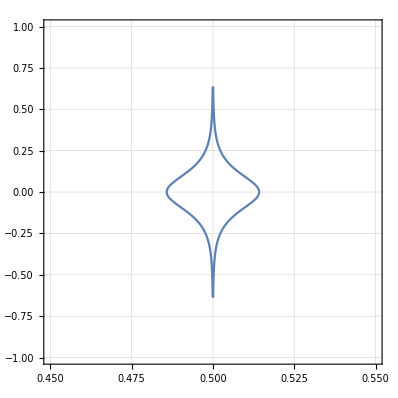

```mathematica
RegionPlot[Abs[bandameio]< 1,{ϵ,0.45,0.55},{y,-1,1},GridLines->Automatic,MaxRecursion->5, PlotStyle->None]
```

```mathematica
listameio={};
For[i=0,i≤ 100, i++;
px = RandomReal[{0.49,0.51}];
py = RandomReal[{-0.1,0.1}];
pt = {px,py};
AppendTo[listameio,pt]]
```

```mathematica
listameio3={};
μ=3.8284
For[i=0,i< Length[listameio],i++;
x0 = listameio⟦i,1⟧;
y0 = listameio⟦i,2⟧;
{x1,y1} = {Re[map[x0,y0,μ]],Im[map[x0,y0,μ]]};
{x2,y2} = {Re[map[x1,y1,μ]],Im[map[x1,y1,μ]]};
{x3,y3} = {Re[map[x2,y2,μ]],Im[map[x2,y2,μ]]};
AppendTo[listameio3,{x3,y3}]];
```

3.8284

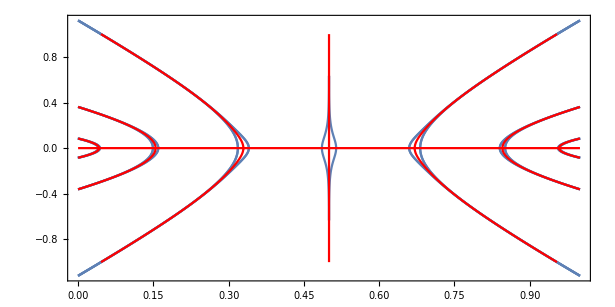

```mathematica
img = Show[pplots, RegionPlot[Abs[bandameio]< 1,{ϵ,0.45,0.55},{y,-1,1},GridLines->Automatic,MaxRecursion->5, PlotStyle->None], ContourPlot[imμ== 0,{x,0,1},{y,-1,1},GridLines->Automatic,ContourStyle->Red, MaxRecursion->5],PlotRange-> Automatic, AspectRatio-> 1/2]
```

```mathematica
Clear[x0]
{maxvalues,minvalues} = {{},{}};
Do[ϵmax =ϵlist⟦2k,1,2,1,2⟧/.x0-> x0s⟦k,2⟧;
If[ϵmax<0,ϵmax =- ϵmax,None];
AppendTo[maxvalues,ϵmax+x0s⟦k,2⟧];
AppendTo[minvalues,-ϵmax+x0s⟦k,2⟧],
{k,{1,2,3}}]
```

```mathematica
f1max = Interpolation[pplotsmax⟦1⟧, InterpolationOrder->2, Method->"Hermite"];
f1min = Interpolation[pplotsmin⟦1⟧, InterpolationOrder->2, Method->"Hermite"];
f2max = Interpolation[pplotsmax⟦2⟧, InterpolationOrder->2, Method->"Hermite"];
f2min = Interpolation[pplotsmin⟦2⟧, InterpolationOrder->2, Method->"Hermite"];
f3max = Interpolation[pplotsmax⟦3⟧, InterpolationOrder->2, Method->"Hermite"];
f3min = Interpolation[pplotsmin⟦3⟧, InterpolationOrder->2, Method->"Hermite"];
fmeio = Interpolation[curvameio, Method->"Hermite"];
```

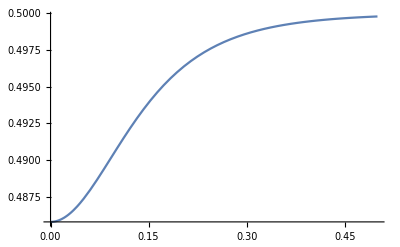

```mathematica
Plot[fmeio[y],{y,0,0.5}]
```

```mathematica
upper = 0.05;
```

```mathematica
bandmeio = {};
For[i=0,i<1000,i++;
py= RandomReal[{0,upper}];
pmax = 0.5;
pmin =fmeio[py];
px = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[bandmeio,{px,a py}]];
```

```mathematica
band1pts = {};
For[i=0,i<10000,i++;
py= RandomReal[{0,upper}];
pmax = Re[f1max[py]];
pmin = Re[f1min[py]];
px = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band1pts,{px,a py}]];
```

InterpolatingFunction::dmval: Input value {0.0198469} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0209186} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
band2pts = {};
For[i=0,i<10000,i++;
py= RandomReal[{0,upper}];
pmax = Re[f2max[py]];
pmin = Re[f2min[py]];
px = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band2pts,{px,a py}]];
```

InterpolatingFunction::dmval: Input value {0.00155931} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000124597} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
band3pts = {};
For[i=0,i<10000,i++;
py= RandomReal[{0,upper}];
pmax = Re[f3max[py]];
pmin = Re[f3min[py]];
px = RandomReal[{pmin,pmax}];
If[RandomInteger[]== 0, a = 1, a=-1];
If[RandomInteger[]== 0, px = 1-px, None];
AppendTo[band3pts,{px,a py}]];
```

InterpolatingFunction::dmval: Input value {0.00605226} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00378619} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

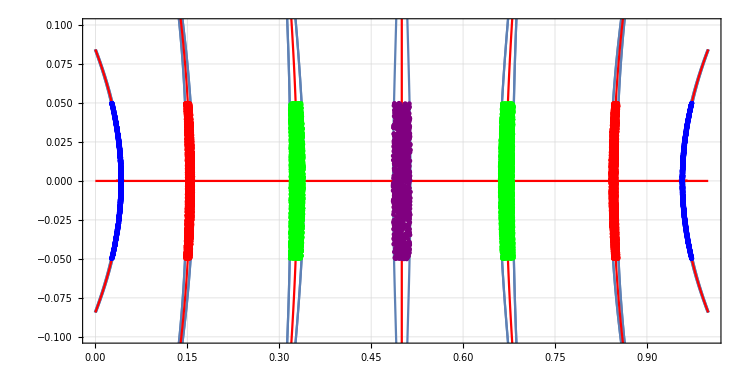

```mathematica
Show[img,ListPlot[band2pts, PlotStyle->Blue],ListPlot[band1pts, PlotStyle->Red],ListPlot[band3pts, PlotStyle->Green],ListPlot[bandmeio, PlotStyle->Purple],GridLines-> Automatic, PlotRange-> {-0.1,0.1}]
```

Mapeamento dos pontos por banda - Tracking do map1 sem imposição de escopo [-∞, +∞]

```mathematica
μ=μ0;
  statsb1={};
For[i=0,i< Length[band1pts],i++;
x = band1pts⟦i,1⟧;
y = band1pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[statsb1,{x,y}]]

  statsb2={};
For[i=0,i< Length[band2pts],i++;
x = band2pts⟦i,1⟧;
y = band2pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[statsb2,{x,y}]]

  statsb3={};
For[i=0,i< Length[band3pts],i++;
x = band3pts⟦i,1⟧;
y = band3pts⟦i,2⟧;
For[j=0,j<3,j++;
{x,y} = {Re[map[x,y,μ]],Im[map[x,y,μ]]}];
AppendTo[statsb3,{x,y}]]
```

```mathematica
Show[img,ListPlot[statsb2, PlotStyle->Blue], ListPlot[statsb3, PlotStyle->Red],ListPlot[statsb1, PlotStyle->Yellow]]
```

Mapeamento dos pontos por banda - Tracking do map1 com imposição de escopo [0, 1]

```mathematica
stats2b1 ={};
points1 = {};
Do[xp = statsb1⟦j,1⟧;
yp =  statsb1⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points1,{xp,yp}],{j,1,Length[statsb1]}] 
stats2b1 = Partition[points1,Length[statsb1]];

stats2b2 ={};
points2 = {};
Do[xp = statsb2⟦j,1⟧;
yp =  statsb2⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points2,{xp,yp}],{j,1,Length[statsb2]}] 
stats2b2 = Partition[points2,Length[statsb2]];

stats2b3 ={};
points3= {};
Do[xp = statsb3⟦j,1⟧;
yp =  statsb3⟦j,2⟧;
If[xp>0, xp = xp - IntegerPart[xp], xp = xp - IntegerPart[xp] + 1];
AppendTo[points3,{xp,yp}],{j,1,Length[statsb3]}] 
stats2b3 = Partition[points3,Length[statsb3]];
```

```mathematica
Show[img,ListPlot[stats2b2, PlotStyle->Blue], ListPlot[stats2b3, PlotStyle->Red],ListPlot[stats2b1, PlotStyle->Yellow]]
```

Mapeamento dos pontos por banda - Tracking do map3 sem imposição de escopo

```mathematica
μ=μ0;
  stats3b1={};
For[i=0,i< Length[band1pts],i++;
x = band1pts⟦i,1⟧;
y = band1pts⟦i,2⟧;
For[j=0,j<3,j++;
{x1,y1} = {Re[map[x,y,μ]],Im[map[x,y,μ]]};
{x2,y2} = {Re[map[x1,y1,μ]],Im[map[x1,y1,μ]]};
{x3,y3} = {Re[map[x2,y2,μ]],Im[map[x2,y2,μ]]};
AppendTo[stats3b1,{x3,y3}]]]

  stats3b2={};
For[i=0,i< Length[band2pts],i++;
x = band2pts⟦i,1⟧;
y = band2pts⟦i,2⟧;
For[j=0,j<3,j++;
{x1,y1} = {Re[map[x,y,μ]],Im[map[x,y,μ]]};
{x2,y2} = {Re[map[x1,y1,μ]],Im[map[x1,y1,μ]]};
{x3,y3} = {Re[map[x2,y2,μ]],Im[map[x2,y2,μ]]};
AppendTo[stats3b2,{x3,y3}]]]

  stats3b3={};
For[i=0,i< Length[band3pts],i++;
x = band3pts⟦i,1⟧;
y = band3pts⟦i,2⟧;
For[j=0,j<3,j++;
{x1,y1} = {Re[map[x,y,μ]],Im[map[x,y,μ]]};
{x2,y2} = {Re[map[x1,y1,μ]],Im[map[x1,y1,μ]]};
{x3,y3} = {Re[map[x2,y2,μ]],Im[map[x2,y2,μ]]};
AppendTo[stats3b3,{x3,y3}]]]

  stats3bmeio={};
For[i=0,i< Length[bandmeio],i++;
x = bandmeio⟦i,1⟧;
y = bandmeio⟦i,2⟧;
For[j=0,j<3,j++;
{x1,y1} = {Re[map[x,y,μ]],Im[map[x,y,μ]]};
{x2,y2} = {Re[map[x1,y1,μ]],Im[map[x1,y1,μ]]};
{x3,y3} = {Re[map[x2,y2,μ]],Im[map[x2,y2,μ]]};
AppendTo[stats3bmeio,{x3,y3}]]]
```

```mathematica
Export["mu10.txt", stats3b1,"Table" ]
```

```mathematica
Export["mu08.txt", stats3b1,"Table" ]
```

```mathematica
Export["mu06.txt", stats3b1,"Table" ]
```

```mathematica
Export["mu04.txt", stats3b1,"Table" ]
```

```mathematica
Export["mu02.txt", stats3b1,"Table" ]
```

mu02.txt

```mathematica
Export["mu00.txt", stats3b1, "Table"]
```

mu00.txt

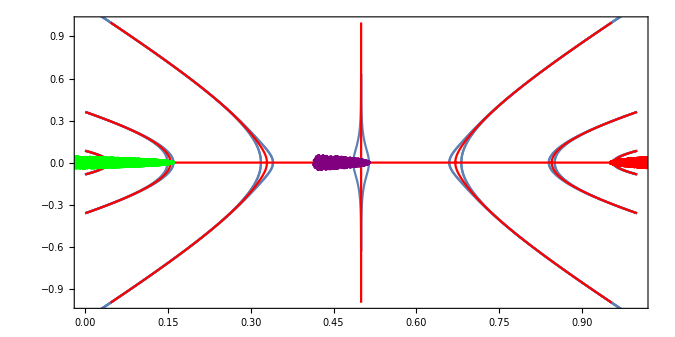

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue],ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Green],ListPlot[stats3bmeio, PlotStyle->Purple],PlotRange-> {{0,1},{-1,1}}]
```

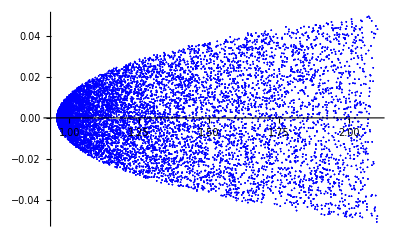

```mathematica
ListPlot[stats3b2, PlotStyle->Blue,PlotRange->All]
```

```mathematica
stats3 = Import["mu02.txt", "Table"];
```

```mathematica
step = 10^-6;
```

```mathematica
xlist = HistogramList[stats3⟦All,1⟧, {0.15,0.16,50step}]⟦1⟧;
peaklist = HistogramList[stats3⟦All,1⟧, {0.15,0.16,50step}]⟦2⟧;
```

```mathematica
ipeak=Flatten[Position[peaklist,Max[peaklist]]]
```

{152}

```mathematica
ipeak2
```

{52}

```mathematica
xlist⟦ipeak⟧
```

{0.15755}

```mathematica
p1⟦ipeak2⟧
```

{3}

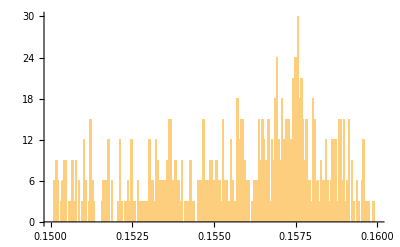

```mathematica
Show[Histogram[stats3⟦All,1⟧, {0.15,0.16,50step}]]
```

```mathematica
peak1 = HistogramList[stats3⟦All,1⟧,{0.15,0.16,step}]⟦1,ipeak1⟧
```

0.150024

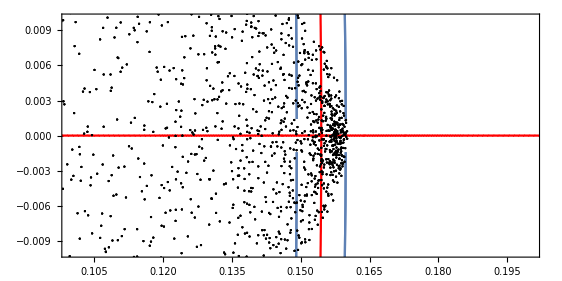

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Black],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

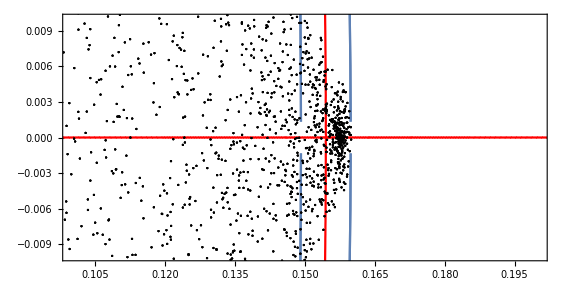

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Black],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

3.8420

-Graphics-

3.8373

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

3.8342

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

3.8330

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

3.8300

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

3.8295

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

3.8289

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

3.8284

-Graphics-

3.8230

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

3.8198 --> q-curves coalescendo para a formação da solução??

```mathematica
Show[img,ListPlot[stats3b2, PlotStyle->Blue], ListPlot[stats3b3, PlotStyle->Red],ListPlot[stats3b1, PlotStyle->Purple],PlotRange-> {{0.1,0.2},{-0.01,0.01}}]
```

-Graphics-

- como deixar expressões “salvas”? --> não dependetes de μ.

```mathematica
lista =Select[stats3b1,0.1<#⟦1⟧ <0.5&];
```

```mathematica
Mean[lista⟦All,1⟧]
```

0.196216

```mathematica
Mean[lista⟦All,1⟧]
```

0.184732